# Response to the Referee Report for “Quantum Interval-Valued Probability: Contextuality and the Born Rule”

### Experimental Data and δ-determinism

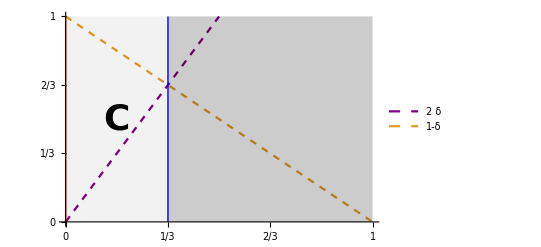
-Graphics-δμ̄

```mathematica
With[{fontSize=18},Labeled[Plot[{2δ,1-δ},{δ,0,1},PlotRange->{{0,1}},PlotLegends->Placed[LineLegend["Expressions",LabelStyle->fontSize],{Right,Center}],PlotStyle->{Directive[Dashed,Purple],Dashed},Ticks->{{0,1/3,2/3,1}},AxesStyle->Directive[Black,fontSize],Epilog->{Opacity[0.05],Polygon[{{1/3,0},{1/3,1},{0,1},{0,0}}],Opacity[0.2],Polygon[{{1/3,0},{1/3,1},{1,1},{1,0}}],Opacity[1],Text[Style["C",2fontSize,Bold],{1/6,1/2}],Thick,Red,Line[{{0,0},{0,1}}],Blue,Line[{{1/3,0},{1/3,1}}]}],{Style[δ,fontSize],Style[OverBar[μ],fontSize]},{Bottom,Left}]]
```

### Mermin-Peres “Magic Square”

```mathematica
NotebookEvaluate[NotebookOpen[FileNameJoin[{NotebookDirectory[],"GleasonDQT.unitary.nb"}]],InsertResults->False];
```

General::obspkg: VectorAnalysis` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
TableForm[Map[MatrixForm,MerminSquare,{2}]]
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1) | (1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)
(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0) | (0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0) | (0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)
(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0) | (0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0) | (0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0)

```mathematica
results0[observable_List,k_Integer]:=With[{p=Position[MerminSquare,observable,{2}]},If[Length[p]==0,Null,If[SubsetQ[{1,2},p⟦1⟧],-1,1]]]
TableForm[Map[results0[#,1]&,MerminSquare,{2}]]
```

-1 | -1 | 1
-1 | -1 | 1
1 | 1 | 1

```mathematica
expectation[observables_List,results_]:=
1/2∑_(k=1)^2 (Times@@(results[#,k]&/@observables))
TableForm[Map[expectation[{#},results0]&,MerminSquare,{2}]]
expectation[{#⟦1⟧,#⟦2⟧},results0]&/@Permutations[MerminSquare⟦1⟧]
expectation[{MerminSquare⟦1,1⟧,MerminSquare⟦1,2⟧},results0]
```

-1 | -1 | 1
-1 | -1 | 1
1 | 1 | 1

{1,-1,1,-1,-1,-1}

1

```mathematica
triad[observables_List,results_]:=With[{sign=(observables⟦1⟧.observables⟦2⟧.Inverse[observables⟦3⟧])⟦1,1⟧},
AllTrue[Permutations[observables],expectation[{#⟦1⟧,#⟦2⟧},results]==sign expectation[{#⟦3⟧},results]&]]
triad[MerminSquare⟦1⟧,results0]
```

True